```mathematica
CollatzSequence[list_]:=Module[{knownEndings,generateSequence},(*Keep track of numbers that lead to known sequences*)knownEndings=<|1->True|>;
generateSequence[n_Integer]:=Module[{fullSequence,newNodes},(*Generate full sequence until we hit a known ending*)fullSequence=NestWhileList[If[EvenQ[#],#/2,3*#+1]&,n,!KeyExistsQ[knownEndings,#]&];
(*Mark all new nodes as leading to known sequences*)newNodes=Most[fullSequence];(*Exclude the final known node*)Do[knownEndings[node]=True,{node,newNodes}];
fullSequence];
Map[generateSequence,list]]
```

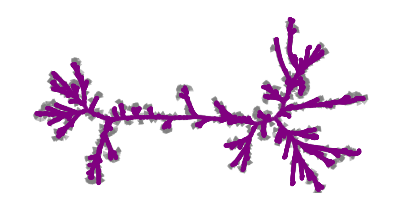

```mathematica
Graph[Flatten[(Rule@@@Partition[#,2,1])&/@CollatzSequence[Range[3000]]],PerformanceGoal->"Speed",GraphLayout->{"SpringElectricalEmbedding"},VertexStyle->Opacity[0.82,Purple],EdgeStyle->Gray]
```

```mathematica
NumElements = 1000

GraphPlot3D[Flatten[(Rule@@@Partition[#,2,1])&/@CollatzSequence[Range[NumElements]]],EdgeStyle->{Yellow,Thick},GraphLayout->"SpringElectricalEmbedding",VertexStyle->Join[Thread[Range[1]->Pink],Thread[Range[1+1,NumElements]->RGBColor[0.97,0.97,0.95]]],VertexSize->100.2151,Background->Black,EdgeRenderingFunction->({Red,Thickness[0.001],Line[#1]}&),VertexRenderingFunction->({Opacity[0.96,RGBColor[0.53,0.81,0.98]],Sphere[#1,1.5]}&)]
```

1000

-Graphics3D-

```mathematica
NN=25;

GraphPlot3D[Flatten[(Rule@@@Partition[#,2,1])&/@CollatzSequence[Range[NN]]],EdgeStyle->{Yellow,Thick},GraphLayout->{"RadialEmbedding","RootVertex"->1},VertexStyle->Join[Thread[Range[1]->Red],Thread[Range[1+1,NN]->RGBColor[0.97,0.97,0.95]]],Background->Yellow,VertexShapeFunction->Join[Thread[Range[1]->"Cuboid"],Thread[Range[1+1,NN]->"Circle"]],VertexLabeling->True]
```

-Graphics3D-

```mathematica
N4= 27

math27=Graph3D[Flatten[(DirectedEdge@@@Partition[#,2,1])&/@CollatzSequence[Range[N4,N4]]],EdgeStyle->{Purple,Thick,Arrowheads[{{Medium,0.75}}]},GraphLayout->{"DiscreteSpiralEmbedding"},VertexStyle->Join[Thread[Range[1]->Red],Thread[Range[N4,N4]->RGBColor[0.97,0.97,0.95]]],Background->White,VertexShapeFunction->Join[Thread[Range[1]->"Cuboid"],Thread[Range[N4,N4]->"Circle"]],VertexLabels->"Name"]
```

27

-Graphics3D-

```mathematica
Graph[Flatten[(Rule@@@Partition[#,2,1])&/@CollatzSequence[Range[15000]]],PerformanceGoal->"Speed",GraphLayout->{"SpringElectricalEmbedding"},EdgeStyle->{Thin,Brown},VertexStyle->Opacity[0.96,White],VertexSize->200,Background->Black]
```

-Graphics-

```mathematica
GraphPlot3D[Flatten[(Rule@@@Partition[#,2,1])&/@CollatzSequence[Range[100]]],EdgeStyle->{Yellow,Thick},GraphLayout->"LayeredEmbedding",VertexStyle->Join[Thread[Range[1]->Red],Thread[Range[1+1,100]->RGBColor[0.97,0.97,0.95]]],VertexSize->1.2151,Background->Black,VertexStyle->Join[Thread[Range[30]->Pink],Thread[Range[1+30,70]->Cyan]],VertexSize->0.00051]
```

-Graphics3D-